```mathematica
√(1/(2*π))ⅇ^(-x^2/(2*σ^2))
```

(ⅇ^(-x^2/(2 σ^2)))/(√(2 π))

```mathematica
Integrate[1/(√(2*π))*1/σ ⅇ^(-x^2/(2*σ^2)),{x,-∞,∞},Assumptions->{σ>0}]
```

1

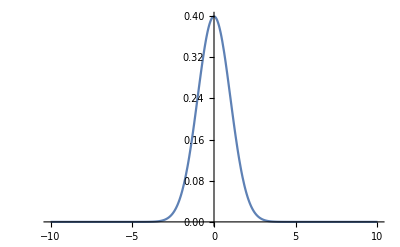

```mathematica
Plot[1/(√(2*π))*1/σ ⅇ^(-x^2/(2*σ^2))/.σ->1,{x,-10,10},PlotRange->Full]
```

```mathematica
Integrate[1/(√(2*π))*1/σ ⅇ^(-x^2/(2*σ^2)),{x,-l/2,l/2},Assumptions->{σ>0,l>0}]
```

Erf[l/(2 √2 σ)]

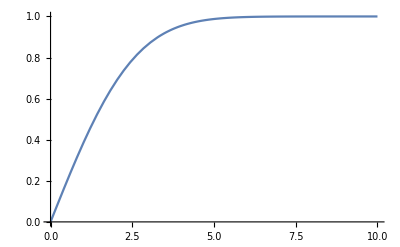

```mathematica
Plot[Erf[l/(2 √2 σ)]/.σ->1,{l,0,10}]
```

```mathematica
Integrate[1/(√(2*π))*1/σ ⅇ^((-(x-μ)^2)/(2*σ^2)),{x,-l/2,l/2}]
```

1/2 (Erf[(l-2 μ)/(2 √2 σ)]+Erf[(l+2 μ)/(2 √2 σ)])

```mathematica
Integrate[1/(√(2*π))*1/σ ⅇ^((-(x-μ)^2)/(2*σ^2)),{x,-l/2,l/2},{μ,-l/2,l/2}]*1/l
```

((-1+ⅇ^(-l^2/(2 σ^2))) √(2/π) σ+l Erf[l/(√2 σ)])/l

```mathematica
((-1+ⅇ^(-l^2/(2 σ^2))) √(2/π) σ+l Erf[l/(√2 σ)])/l/.l->cr/nn
```

(nn ((-1+ⅇ^(-cr^2/(2 nn^2 σ^2))) √(2/π) σ+(cr Erf[cr/(√2 nn σ)])/nn))/cr

```mathematica
FullSimplify[(nn ((-1+ⅇ^(-cr^2/(2 nn^2 σ^2))) √(2/π) σ+(cr Erf[cr/(√2 nn σ)])/nn))/cr,Assumptions->{σ>0,n>=1}]
```

((-1+ⅇ^(-cr^2/(2 nn^2 σ^2))) nn √(2/π) σ)/cr+Erf[cr/(√2 nn σ)]

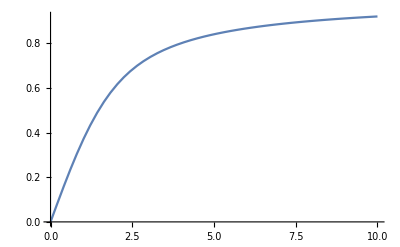

```mathematica
Plot[((-1+ⅇ^(-l^2/2)) √(2/π)+l Erf[l/(√2)])/l,{l,0,10}]
```

```mathematica
0.065*2*π
```

0.408407

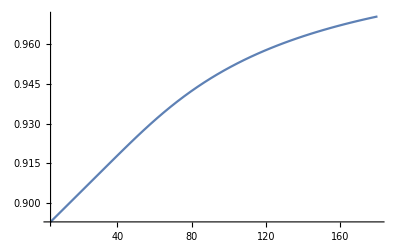

```mathematica
Plot[1-η*(nn ((-1+ⅇ^(-cr^2/(2 nn^2 σ^2))) √(2/π) σ+(cr Erf[cr/(√2 nn σ)])/nn))/cr/.{σ->0.065*0.05,cr->0.065*2*π,η->0.11},{nn,4,180},PlotRange->Full]
```

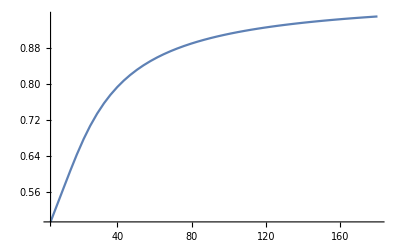

```mathematica
Plot[1-η*(nn ((-1+ⅇ^(-cr^2/(2 nn^2 σ^2))) √(2/π) σ+(cr Erf[cr/(√2 nn σ)])/nn))/cr/.{σ->+0.01,cr->0.065*2*π,η->+0.55},{nn,4,180},PlotRange->Full]
```

```mathematica
Integrate[ⅇ^((-(x-μ)^2)/(2*1)),{x,-l/2,l/2},{μ,(-4*l)/2,(4*l)/2}]*1/l
```

(2 ⅇ^(-(25 l^2)/8)-2 ⅇ^(-(9 l^2)/8)+l √(π/2) (-3 Erf[(3 l)/(2 √2)]+5 Erf[(5 l)/(2 √2)]))/l

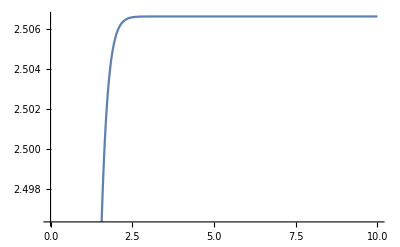

```mathematica
Plot[(2 ⅇ^(-(25 l^2)/8)-2 ⅇ^(-(9 l^2)/8)+l √(π/2) (-3 Erf[(3 l)/(2 √2)]+5 Erf[(5 l)/(2 √2)]))/l,{l,0,10}]
```

```mathematica
Integrate[√(1/(2*π))ⅇ^((-(x-μ)^2)/(2*1)),{μ,-l/2,l/2}]*1/l
```

(-Erf[(-l/2+x)/(√2)]+Erf[(l/2+x)/(√2)])/(2 l)

```mathematica
Manipulate[Plot[(-Erf[(-l/2+x)/(√2)]+Erf[(l/2+x)/(√2)])/(2 l),{x,-10,10},PlotRange->Full],{l,0.001,10}]
```

```mathematica
Solve[-0.055*(alin-0.50)+0.058==0.065,alin]
```

{{alin→0.372727}}

```mathematica
Solve[0.055*(alin-3.35)+0.058==0.065,alin]
```

{{alin→3.47727}}